```mathematica
m1=1000000;
m2= 1;
m3=0.000001;
g=0.0001;
```

```mathematica
r1=NDSolve[{x1''[t]==-g*m2*(x1[t]-x2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^1.5,
y1''[t]==-g*m2*(y1[t]-y2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^1.5,
x3''[t]==-g m2 *(x3[t]-x2[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^1.5-g m1*(x3[t]-x1[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^1.5,
y3''[t]==-g m2 *(y3[t]-y1[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^1.5-g m1*(y3[t]-y1[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^1.5,
x2''[t]==-x1''[t]/m2*m1-x3''[t]/m2*m3,
y2''[t]==-y1''[t]/m2*m1-y3''[t]/m2*m3,
x1[0]==0,
y1[0]==0,
x1'[0]==0,
y1'[0]==0,
x2[0]==10,
y2[0]==0,
x2'[0]==0,
y2'[0]==3,
x3[0]==9.99,
y3[0]==0,
x3'[0]==0,
y3'[0]==6
},{x1,y1, x2, y2,x3,y3},{t,0,100}];
```

```mathematica
sunx=x1/.First[r1];
suny=y1/.First[r1];
earthx=x2/.First[r1];
earthy=y2/.First[r1];
moonx=x3/.First[r1];
moony=y3/.First[r1];
```

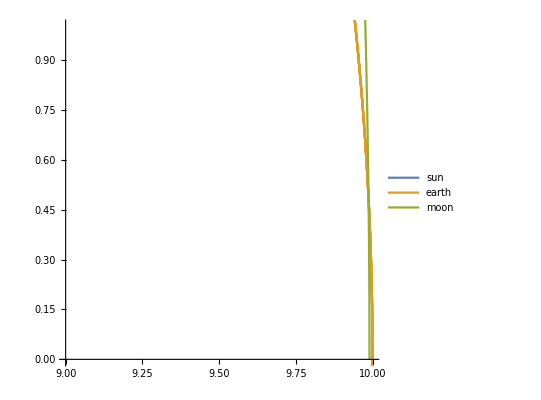

```mathematica
ParametricPlot[{{sunx[t],suny[t]},{earthx[t],earthy[t]},{moonx[t],moony[t]}},{t,0,100}, PlotRange->{{9,10},{0,1}}, PlotLegends->{"sun", "earth","moon"}]
```